# f.figure.rencon2.strange.baryons-all.interpolate.ci-1.5.nb

```mathematica
NotebookFileName[]
```

使用插值的方法，处理图像数据，生成插值函数，然后重新画图，这样就可以研究每个图符号改变的影响了

## initial

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

## global setting

选定用来绘图的数据配置

```mathematica
fontsize`frame=8;
imagesize=Scaled[.6];
```

## data initial

## import origin figs

{Λ, ci}→

{0.8,1.0} l1c1,{0.9,1.0} l2c1,{1.0,1.0} l3c1,

{0.8,1.5} l1c2,{0.9,1.5} l2c2,{1.0,1.5} l3c2

```mathematica
fig`calc`baryons`ge`total`origin=
(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.separate.baryons.ge.tot.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`gm`total`origin=(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.separate.baryons.gm.tot.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`ge`total`origin//Dimensions
fig`calc`baryons`gm`total`origin//Dimensions
```

{1,8,11,2}

{1,8,11,2}

## extract data

```mathematica
{data`f1[x_],data`f1[y_]}^:=data`f2[Join[x,y]]
```

```mathematica
{data`f1[x_]}^:=data`f2[x]
```

将Line中出现的数据用data`f1做tag，并且通过赋上值的方式合并到data`f2

f 是format的意思

fig`calc`baryons`ge`total`origin,{config,io,if,treeloop},{6,8,11,2}

```mathematica
fun`data`extract[fig`calc`baryons`ge`total`origin_]:=Table[
Cases[
fig`calc`baryons`ge`total`origin⟦config,io,if,treeloop⟧
,Line[x_]:>data`f1[x],10(*level*)
]
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
]
```

```mathematica
data`calc`baryons`gegm`total={
fun`data`extract[fig`calc`baryons`ge`total`origin],
fun`data`extract[fig`calc`baryons`gm`total`origin]
};
```

```mathematica
data`calc`baryons`gegm`total//Dimensions
```

data`calc`baryons`gegm`total,{2,1,8,11,2}, {gegm,config,io,if,treeloop}

## interpolate

## interpolate functions

```mathematica
fun`interp`calc`baryons`gegm`total=Table[

data`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧/.data`f2->Interpolation

,{gegm,1,2,1}
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
];
```

```mathematica
fun`interp`calc`baryons`gegm`total//Dimensions
```

## left boundarys

求出每个图的左边界

```mathematica
boundary`left`if=Table[
Min[(data`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧/.data`f2->Identity)⟦All,1⟧]
,{gegm,1,2,1}
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
];
```

求出所有图左边界中的最大值

```mathematica
boundary`left=Table[
Max[boundary`left`if⟦gegm,config,io,All,treeloop⟧]
,{gegm,1,2,1}
,{config,1,1,1}
,{io,1,8,1}
,{treeloop,1,2,1}
];
```

## draw

改变每个图的符号，然后求和作图

```mathematica
pre`sign={
{(*+++++++++++++++++1*)
1,1,1(*3*),
1,(*4*)1,(*5*)
1,1,1,(*8*)1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++2*)
1,1,1(*3*),
1,(*4*)1,(*5*)
1,1,1,(*8*)-1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++3*)
-1,-1,-1(*3*),
-1,(*4*)-1,(*5*)
1,1,1,(*8*)1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++4*)
1,1,1(*3*),
1,(*4*)1,(*5*)
-1,-1,-1,(*8*)-1,(*9*)
-1,-1(*11*)
},
{(*+++++++++++++++++5*)
-2,1,1(*3*),
1,(*4*)1,(*5*)
-1,-1,-1,(*8*)0,(*9*)
-1,-1(*11*)
}
};
```

gegm=1;config=1;io=2;if=Span[1,11];treeloop=2;

```mathematica
fun`draw[pre`sign_,fun`interp`calc`baryons`gegm`total_,gegm_,config_,io_,if_,treeloop_]:=CompoundExpression[
tef=fun`interp`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧,
te`left=boundary`left⟦gegm,config,io,treeloop⟧,
Plot[
Evaluate[
Total[
Through[tef[Q2]]*pre`sign
]
],
{Q2,te`left,1},
PlotRange->All,
ImageSize->Medium,
PlotStyle->Thin,
PlotLegends->Range[Dimensions[tef]]
]
]
```

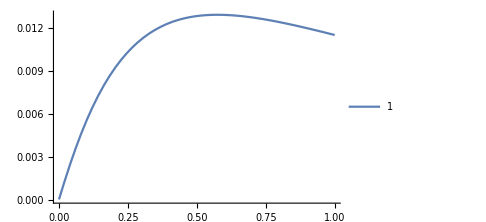

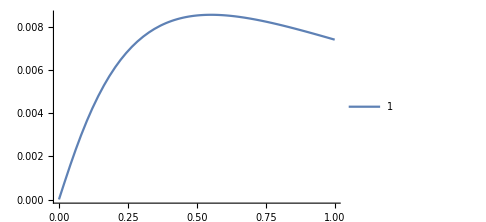

```mathematica
gegm=1;config=1;io=7;if=Span[1,11];treeloop=2;
fun`draw[pre`sign⟦1⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop]
fun`draw[pre`sign⟦2⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop]
```